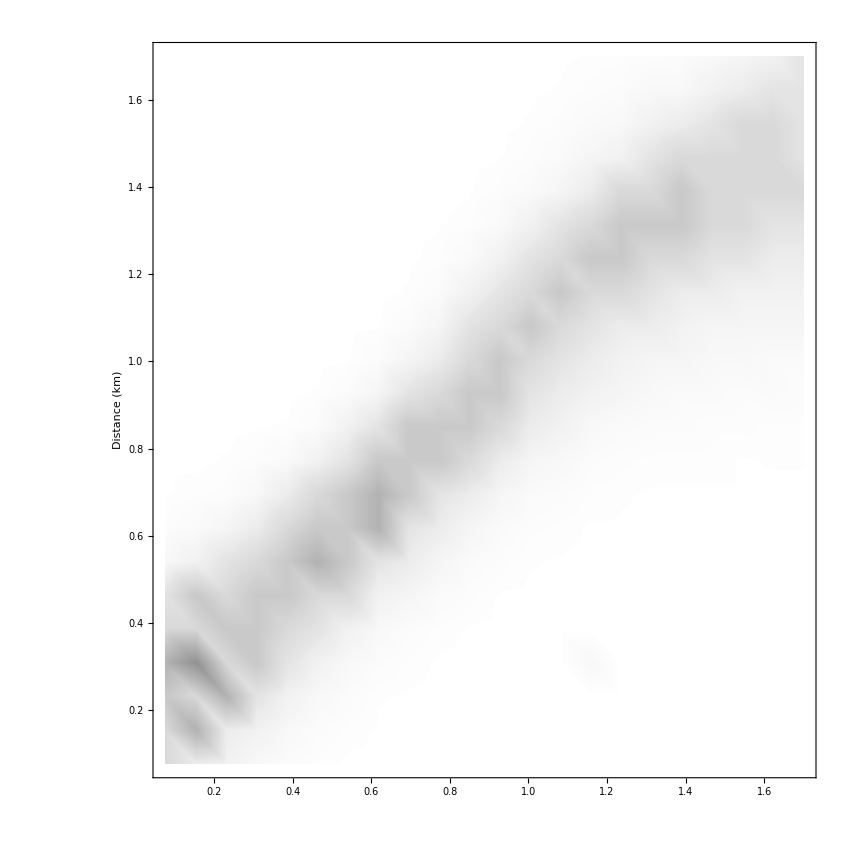

```mathematica
SOLme = Import["Migration_matrixTracks.dat"];
TracksTab = Table[{N[(*10^(0+Log10[50]*i/22)*)Log10[50]*i/22],N[(*10^(0+Log10[50]*j/22)*)Log10[50]*j/22],SOLme[[i,j]]},{i,1,22},{j,1,22}];
OscUVme=ListContourPlot[Flatten[TracksTab,1] , FrameTicks-> Automatic,Contours-> 100, ContourLines-> False, ColorFunctionScaling->False, 
ColorFunction->(Blend[{{0.0,White},{1.,Black}},#]&),(*ColorFunction->(Blend[{{-0.05,Darker[Blue]},{0.03,Red}},#]&),*)
(*PlotLegends->BarLegend[{"TemperatureMap",{-0.06,0.08}},LabelStyle-> Directive[FontSize-> 32,Black,FontFamily-> "Times"]], *)ImageSize->850,BaseStyle-> {Medium,FontFamily-> "Times",FontSize-> 42},FrameTicksStyle->Thickness[0.0018],FrameStyle->Directive[Black,Thickness[0.0018]],PlotRange->All,
FrameLabel-> {{Text[Style["Distance (km)",42, FontFamily->"Times"]],None},{(*Text[Style["E(GeV)",32, FontFamily->"Times"]]*)None,None}},ImagePadding->{{130,20},{95,10}}]
```

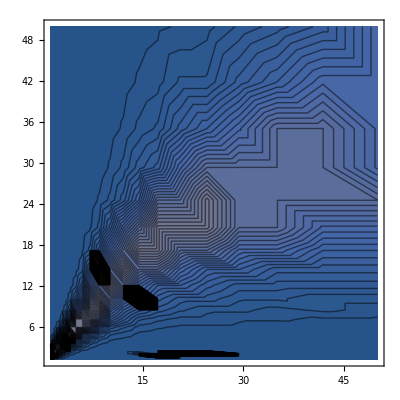

```mathematica
ListContourPlot[Flatten[TracksTab,1],FrameTicks->Automatic,Contours->100,PlotRange->All ,ColorFunctionScaling->False]
```